```mathematica
(*1*)
number =RandomInteger[{0,20}]
PrimeQ[number]
```

7

True

```mathematica
Realnumber = RandomReal[{-200,200}]
```

139.571

```mathematica
Positive[Realnumber]
```

True

```mathematica
(*2*)
(* = znak przypisujący wartość dla zmiennej
== zwraca True/False, gdy porównujemy czy wartości są sobie równe. Znak nie jest wrażliwy na typy
=== zwraca True/False, gdy porównujemy czy wartości są identyczne. Znak jest wrażliwy na typy*)
x=3
y=3.
x==y
x===y
```

3

3.

True

False

```mathematica
(*3*)
```

```mathematica
f[0]=0;f[1]=1;
f[n_]:=f[n]=f[n-1]+f[n-2]

Fib =Array[f, 10]
```

{1,1,2,3,5,8,13,21,34,55}

```mathematica
g[0]=3;
g[n_] :=g[n]=g[n-1]^2
Array[g,5]
```

```mathematica
{9,81,6561,43046721,1853020188851841}
(*4*)
(*
=, := w pierwszym przypadku wartość funkcji jest obliczana przy defi.1cniowaniu funkcji,w
drugim-wartość funkcji jest obliczana przy wywoływaniu funkcji dla argumentu. := zadziała tylko gdy mamy podane argumenty
*)
(*5*)
ListPlot[Labeled[Fib,\[FreakedSmiley]],LabelingFunction->(#1&), AxesLabel->{n, a[n]}, Joined->True, Mesh->All, MeshStyle->Red,Background->LightBlue]
```

{9,81,6561,43046721,1853020188851841}

-Graphics-

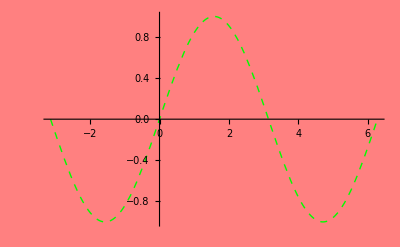

```mathematica
(*6*)
Plot[Sin[x],{x,-π,2 π}, Background ->Pink, PlotStyle->{Green,Thick, Dashed}]
```

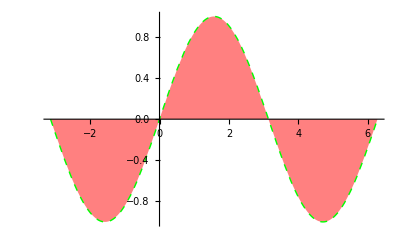

```mathematica
Plot[Sin[x],{x,-π,2 π},Filling ->Axis,FillingStyle->Pink, PlotStyle->{Green,Thick, Dashed}]
```

```mathematica
(*7*)
```

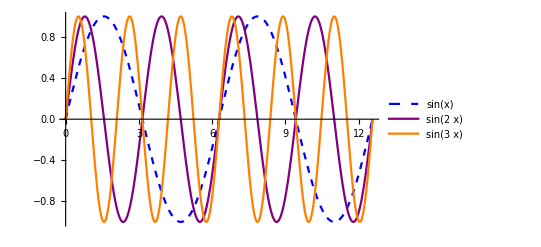

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,4 Pi},PlotStyle ->{{Blue,Dashed},  {Purple,Thick}, Orange}, PlotLegends->"Expressions"]
```

```mathematica
(*8*)
```

```mathematica
Plot[Sin[x^2+y^2],{x,-π,2 π},{y, -π,2 π},Filling ->Axis,FillingStyle->Pink, PlotStyle->{Green,Thick, Dashed}]
```

Plot::nonopt: Options expected (instead of {y,-π,2 π}) beyond position 2 in Plot[Sin[x^2+y^2],{x,-π,2 π},{y,-π,2 π},Filling→Axis,FillingStyle→Pink,PlotStyle→{Green,Thick,Dashed}]. An option must be a rule or a list of rules.

```mathematica
Plot3D[Sin[x^2+y^2],{x,-π, π},{y,-π, π}, PlotStyle->Green, MeshStyle->None, Axes->None]
```

-Graphics3D-

```mathematica
(*9*)
```

```mathematica
ParametricPlot3D[{Cos[t]*(3+Cos[u]),Sin[t]*(3+Cos[u]),Sin[u]},{u,0,2 Pi}, {t,0,2 Pi}, PlotStyle->Pink]
```

-Graphics3D-

```mathematica
(*10*)
```

```mathematica
Animate[Plot[E^Sin[t*x],{x,-Pi,Pi},PlotRange->{0,3}],{t, 0,4},AnimationRunning->False ]
```

```mathematica
Animate[Plot[E^Sin[t*x],{x,-Pi,Pi},PlotRange->{0,3}],{t,0,8,2}, AnimationRunning->False ]
```

```mathematica
Animate[Plot[E^Sin[t*x],{x,-Pi,Pi}, PlotRange->{0,3}],{t,{0,4,7,8}}, AnimationRunning->False ]
```

```mathematica
(*11*)
```

```mathematica
Animate[Plot3D[E^a*Sin[x+y]+b*Cos[x-y],{x,0,2*Pi}, {y,0,2*Pi},PlotRange->{0,9}],{a,0,1},{b,0,9,2}, AnimationRunning->False ]
```